## Δ Orientation in ℂ

Determining the orientation of a loop through three points in ℂ.

Here is away using the determinant.

0.49607

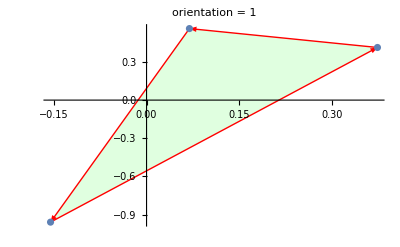

```mathematica
{p1,p2,p3}=RandomComplex[{-1-I,1+I},3];
{u1,u2}={p1,p3}-p2;
orient=-Det[ReIm[{u1,u2}]]
ListPlot[ReIm[{p1,p2,p3}],
Prolog->{
{LightGreen,Polygon[ReIm[{p1,p2,p3}]]},
{Red, Map[Arrow,ReIm[{{p1,p2},{p2,p3},{p3,p1}}]]}
},
PlotLabel->StringForm["orientation = ``",Sign[orient]]]
```

## Hermite Interpolation on a line ∫_a^b f(z)dz

### (0,1) Hermite cubics

On (0,1) the nodal Hermite interpolation polynomials are

```mathematica
Clear[c,x,f,p]
p=3;
f[x_]=Sum[c[i] x^i,{i,0,p}];
g[x_]=Map[Factor[f[x]/.Solve[#]]&,
{
{f[0]==1,f'[0]==0,f[1]==0,f'[1]==0},
{f[0]==0,f'[0]==1,f[1]==0,f'[1]==0},
{f[0]==0,f'[0]==0,f[1]==1,f'[1]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==1}
}];
TabView[{
"f"->Plot[Evaluate[g[x]],{x,0,1},PlotLegends->Automatic],
"f'"->Plot[Evaluate[g'[x]],{x,0,1},PlotLegends->Automatic]
}]
```

12

### (0,1) Hermite cubics with central node.

On (0,1) the nodal Hermite interpolation polynomials are

```mathematica
Clear[c,x,f,p]
p=5;
f[x_]=Sum[c[i] x^i,{i,0,p}];
g[x_]=Map[Factor[f[x]/.Solve[#]]&,
{
{f[0]==1,f'[0]==0,f[1]==0,f'[1]==0,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==1,f[1]==0,f'[1]==0,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==1,f'[1]==0,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==1,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==0,f[1/2]==1,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==0,f[1/2]==0,f'[1/2]==1}
}];
TabView[{
"f"->Plot[Evaluate[g[x]],{x,0,1},PlotLegends->Automatic],
"f'"->Plot[Evaluate[g'[x]],{x,0,1},PlotLegends->Automatic]
}]
```

12

### (0,1) Hermite reciprocal cubics

On (0,1) I can use things other than polynomials.  I could use “symmetric” Laurent polynomials
about some point lying off the line.  This does not work!

```mathematica
Clear[c,a,x,f,p]
r=2;
f[x_]=Sum[c[i](x-(1/2+a ⅈ)  )^i ,{i,-r,r}]
Solve[{f[0]==1,f'[0]==0,f[1]==0,f'[1]==0}]
Solve[{f[0]==0,f'[0]==1,f[1]==0,f'[1]==0}]
```

c[-2]/(-1/2-ⅈ a+x)^2+c[-1]/(-1/2-ⅈ a+x)+c[0]+(-1/2-ⅈ a+x) c[1]+(-1/2-ⅈ a+x)^2 c[2]

{{c[-2]→1/16 (1+4 a^2)^2 (2 ⅈ a+c[2]),c[-1]→1/8 (1+4 a^2) (-1+12 a^2-8 ⅈ a c[2]),c[0]→-1/2 ⅈ (ⅈ+a+12 a^3-ⅈ c[2]-12 ⅈ a^2 c[2]),c[1]→1/2 (-1-4 a^2+8 ⅈ a c[2])}}

{{c[-2]→1/32 (1+4 a^2)^2 (1+2 ⅈ a+2 c[2]),c[-1]→1/16 (1+4 a^2) (-1-8 ⅈ a+12 a^2-16 ⅈ a c[2]),c[0]→-1/8 ⅈ (-ⅈ-2 a-20 ⅈ a^2+24 a^3-4 ⅈ c[2]-48 ⅈ a^2 c[2]),c[1]→1/4 (1+4 ⅈ a-4 a^2+16 ⅈ a c[2])}}

```mathematica
g[x_]=Map[Factor[f[x]/.Solve[#]]&,
{
{f[0]==1,f'[0]==0,f[1]==0,f'[1]==0},
{f[0]==0,f'[0]==1,f[1]==0,f'[1]==0},
{f[0]==0,f'[0]==0,f[1]==1,f'[1]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==1}
}]
```

{{-(-1+x)^2/(-1+2 x)},(-c[-1]+ⅈ a c[0]-x c[0]+a^2 c[1]+2 ⅈ a x c[1]-x^2 c[1])/(ⅈ a-x),{x^2/(-1+2 x)},(-c[-1]+ⅈ a c[0]-x c[0]+a^2 c[1]+2 ⅈ a x c[1]-x^2 c[1])/(ⅈ a-x)}

```mathematica
TabView[{
"f"->Plot[Evaluate[Re[g[x]]],{x,0,1},PlotLegends->Automatic],
"f'"->Plot[Evaluate[g'[x]],{x,0,1},PlotLegends->Automatic]
}]
```

{1/((0.-0.2 ⅈ)+1. x)1. (1. c[-1]-(0.+0.2 ⅈ) c[0]+1. x c[0]-(0.04+0. ⅈ) c[1]-(0.+0.4 ⅈ) x c[1]+1. x^2 c[1]),1/((0.-0.2 ⅈ)+1. x)1. (1. c[-1]-(0.+0.2 ⅈ) c[0]+1. x c[0]-(0.04+0. ⅈ) c[1]-(0.+0.4 ⅈ) x c[1]+1. x^2 c[1]),1/((0.-0.2 ⅈ)+1. x)1. (1. c[-1]-(0.+0.2 ⅈ) c[0]+1. x c[0]-(0.04+0. ⅈ) c[1]-(0.+0.4 ⅈ) x c[1]+1. x^2 c[1]),1/((0.-0.2 ⅈ)+1. x)1. (1. c[-1]-(0.+0.2 ⅈ) c[0]+1. x c[0]-(0.04+0. ⅈ) c[1]-(0.+0.4 ⅈ) x c[1]+1. x^2 c[1])}

12

```mathematica
¶I
```

## Pade Approximation

To compute  f[x]≈p(x)/q(x) with p(x) of degree m and q(x) of degree n with q(0)=1 all I do is clear the fraction and match coefficients.  It looks like this
	q(x)f(x)-p(x)=0+0 x+…+0 x^m+0 x^(m+1)+…+0 x^(m+n)+O(x^(n+m+1))
The m+1 coefficients in the numerator p(x) are directly determined by the first  m+1 equations.  The n unknown coefficients in the denominator q(x) are determined by the next n equations.  The coefficients of q(x)*f(x) are the convolution of the coefficients of q(x) and a sufficiently long truncation of the power series for f.  Some parts of the literature tends to use any element of the null space of the n×(m+1) Toeplitz matrix
	T=(f[m+1] | f[m] | … | f[1]
f[m+2] | f[m+1] |   | f[2]
⋮ |   |   |  
f[m+n] |   |   |  )
as the coefficients of the denominator.  I am making the decision to use the solution q(x)=1+q_1 x+…  I am making the decision that I am using raw polynomials and making the i! scalings to and from the power series representations if (and when) needed.

```mathematica
Clear[m,n,f,fs,p,ps,q,qs]
{m,n}={3,3};
{fs,ps,qs}={Array[f,m+n+1,0],
Array[p,m+1,0],
Array[q,n+1,0]};
CoeffToPoly[coeffs_List,x_]:=Sum[coeffs⟦i⟧x^(i-1),{i,Length[coeffs]}]
Eqs=CoefficientList[CoeffToPoly[fs,x]CoeffToPoly[qs,x]-CoeffToPoly[ps,x],x]⟦1;;m+n+1⟧;
TableForm[Eqs⟦1;;n+1⟧,TableHeadings->{Table[x^i,{i,0,n}],Automatic}]
TableForm[Eqs⟦n+2;;m+n+1⟧,TableHeadings->{Table[x^i,{i,n+1,m+n}],Automatic}]
```

1 | -p[0]+f[0] q[0]
x | -p[1]+f[1] q[0]+f[0] q[1]
x^2 | -p[2]+f[2] q[0]+f[1] q[1]+f[0] q[2]
x^3 | -p[3]+f[3] q[0]+f[2] q[1]+f[1] q[2]+f[0] q[3]

x^4 | f[4] q[0]+f[3] q[1]+f[2] q[2]+f[1] q[3]
x^5 | f[5] q[0]+f[4] q[1]+f[3] q[2]+f[2] q[3]
x^6 | f[6] q[0]+f[5] q[1]+f[4] q[2]+f[3] q[3]

```mathematica
Solve[
Eqs⟦-n;;-1⟧==ConstantArray[0,{n}],
qs]
```

```mathematica
Solve[Table[
Eqs⟦i⟧==0,{i,Length[Eqs]}],Join[qs⟦2;;m+1⟧,ps]]
```

{{q[1]→-(f[2] f[3]-f[1] f[4])/(f[2]^2-f[1] f[3]),q[2]→-(f[3]^2-f[2] f[4])/(-f[2]^2+f[1] f[3]),p[0]→f[0],p[1]→-(f[1] f[2]^2-f[1]^2 f[3]-f[0] f[2] f[3]+f[0] f[1] f[4])/(-f[2]^2+f[1] f[3]),p[2]→-(f[2]^3-2 f[1] f[2] f[3]+f[0] f[3]^2+f[1]^2 f[4]-f[0] f[2] f[4])/(-f[2]^2+f[1] f[3])}}

```mathematica
Map[MatrixForm,CoefficientArrays[
CoefficientList[CoeffToPoly[fs,x]CoeffToPoly[qs,x]-CoeffToPoly[ps,x],
x]⟦m+2;;m+n+1⟧,
Array[q,n]]]
```

{(f[4]
f[5]
f[6]
f[7]
f[8]),(f[3] | f[2] | f[1] | f[0] | 0
f[4] | f[3] | f[2] | f[1] | f[0]
f[5] | f[4] | f[3] | f[2] | f[1]
f[6] | f[5] | f[4] | f[3] | f[2]
f[7] | f[6] | f[5] | f[4] | f[3])}

```mathematica
?Series
```

```mathematica
{m,n}={3,2};
Simplify[
CoefficientList[Series[q[x] f[x],{x,0, n+m+1}],x]*Table[i!,{i,0, n+m+1}]
]
```

{f[0] q[0],q[0] f'[0]+f[0] q'[0],2 f'[0] q'[0]+q[0] f''[0]+f[0] q''[0],3 q'[0] f''[0]+3 f'[0] q''[0]+q[0] f^(3)[0]+f[0] q^(3)[0],6 f''[0] q''[0]+4 q'[0] f^(3)[0]+4 f'[0] q^(3)[0]+q[0] f^(4)[0]+f[0] q^(4)[0],10 q''[0] f^(3)[0]+10 f''[0] q^(3)[0]+5 q'[0] f^(4)[0]+5 f'[0] q^(4)[0]+q[0] f^(5)[0]+f[0] q^(5)[0],20 f^(3)[0] q^(3)[0]+15 q''[0] f^(4)[0]+15 f''[0] q^(4)[0]+6 q'[0] f^(5)[0]+6 f'[0] q^(5)[0]+q[0] f^(6)[0]+f[0] q^(6)[0]}

```mathematica
CoefficientList[Series[q[x],{x,0, n}],x]
```

{q[0],q'[0],q''[0]/2}

```mathematica
Clear[f]
{n,m}={3,3};
ToeplitzMatrix[
Table[Derivative[i][f][a],{i,m+1,m+n}],
Table[Derivative[i][f][a],{i,m+1,1,-1}]
]//MatrixForm
```

(f^(4)[a] | f^(3)[a] | f''[a] | f'[a]
f^(5)[a] | f^(4)[a] | f^(3)[a] | f''[a]
f^(6)[a] | f^(5)[a] | f^(4)[a] | f^(3)[a])

The indexing in this computation is a pain.  
 (f[4] | f[3] | f[2] | f[1]
f[5] | f[4] | f[3] | f[2]
f[6] | f[5] | f[4] | f[3])

## Diagonal Pade Approximation

To compute  f[x]≈p(x)/q(x) with p(x) of degree n and q(x) of degree n+1 with q(0)=1 all I do is clear the fraction and match coefficients.  It looks like this
	q(x)f(x)-p(x)=0+0 x+…
The first n+1 terms determines p(x) the next n determine q(x).

Here is a small demo.

```mathematica
Clear[f,x,n]
n=3;
Eqs=CoefficientList[
Expand[
Sum[q[i] x^i,{i,0,n}]*Sum[f[i] x^i,{i,0,2n}]-Sum[p[i] x^i,{i,0,n}]
],x];
{TableForm[
Eqs⟦1;;n+1⟧,
TableHeadings->{Range[0,n]}],
TableForm[
Eqs⟦n+2;;2n+1⟧,
TableHeadings->{Range[n+1,2n]}]}
T=ToeplitzMatrix[{f[4],f[5],f[6]},{f[4],f[3],f[2],f[1]}];
{MatrixForm[T],MatrixForm[T.Table[q[i],{i,0,n}]]}
```

{0 | -p[0]+f[0] q[0]
1 | -p[1]+f[1] q[0]+f[0] q[1]
2 | -p[2]+f[2] q[0]+f[1] q[1]+f[0] q[2]
3 | -p[3]+f[3] q[0]+f[2] q[1]+f[1] q[2]+f[0] q[3],4 | f[4] q[0]+f[3] q[1]+f[2] q[2]+f[1] q[3]
5 | f[5] q[0]+f[4] q[1]+f[3] q[2]+f[2] q[3]
6 | f[6] q[0]+f[5] q[1]+f[4] q[2]+f[3] q[3]}

{(f[4] | f[3] | f[2] | f[1]
f[5] | f[4] | f[3] | f[2]
f[6] | f[5] | f[4] | f[3]),(f[4] q[0]+f[3] q[1]+f[2] q[2]+f[1] q[3]
f[5] q[0]+f[4] q[1]+f[3] q[2]+f[2] q[3]
f[6] q[0]+f[5] q[1]+f[4] q[2]+f[3] q[3])}

### Code

I am going to build code for a diagonal Pade approximant from a function

```mathematica
Clear[AAASPade]
AASPade[f_,a_,n_]:= Module[{ff,T,pp,qq},
ff=Table[Derivative[i][f][a]/i!,{i,0, 2n}];
T=ToeplitzMatrix[ff[[n+2;;-1]],Reverse[ff⟦2;;n+2⟧]];
NullSpace[T]
]
```

```mathematica
f[x_]:=1/(1+0 x^2+x^4)
MatrixForm[AASPade[f,0,2]]
```

(0 | 0 | 1
0 | 1 | 0)

```mathematica
({{f[4], f[3], f[2], f[1]}, {f[5], f[4], f[3], f[2]}, {f[6], f[5], f[4], f[3]}})
```

```mathematica
|
```

```mathematica
D[Exp[x],{x,2}]
```

ⅇ^x

### Fast Matrix Aside.

```mathematica
n=3;
qq=Table[q[i],{i,0,n}];
ff=Table[f[i],{i,0,2n+1}];
TableForm[Hmm=ListConvolve[qq,ff]⟦2;;n+1⟧,
TableHeadings->{Range[n+1,2n]}]
```

```mathematica
MatrixForm[Fred=Hmm⟦All,2;;-1⟧]
```

(f[3] | f[2] | f[1]
f[4] | f[3] | f[2]
f[5] | f[4] | f[3])

The inverse of a circulant matrix is simple

```mathematica
m=3;c=RandomReal[{-1,1},m];
v=Fourier[c,FourierParameters->{1, -1}];
X=N[FourierMatrix[m]];
Fred=X.DiagonalMatrix[v].ConjugateTranspose[X];
CMat=ToeplitzMatrix[c,RotateRight[Reverse[c]]];
MatrixForm[CMat]
MatrixForm[Chop[Fred]]
```

(0.847123 | 0.881599 | 0.545968
0.545968 | 0.847123 | 0.881599
0.881599 | 0.545968 | 0.847123)

(0.847123 | 0.881599 | 0.545968
0.545968 | 0.847123 | 0.881599
0.881599 | 0.545968 | 0.847123)

```mathematica
n=3;
tc=RandomReal[{-1,1},n]; tr=Join[tc⟦{1}⟧,RandomReal[{-1,1},n-1]];
T=ToeplitzMatrix[tc,tr];
bc=Join[{0.0},Reverse[tr⟦2;;-1⟧]];
br=Join[{0.0},Reverse[tc⟦2;;-1⟧]];
bc⟦1⟧=br⟦1⟧=0.0;
B=ToeplitzMatrix[bc,br];
MatrixForm[BigCMat=ArrayFlatten[({{T, B}, {B, T}})]];
tBigc=Join[tc,bc];
MatrixForm[ToeplitzMatrix[tBigc,RotateRight[Reverse[tBigc]]]];
X=FourierMatrix[2m];
Norm[
BigCMat-X.DiagonalMatrix[Fourier[tBigc,FourierParameters->{1, -1}]].ConjugateTranspose[X]]
```

9.64924×10^-16

```mathematica
?ToeplitzMatrix
```

```mathematica
Eqs
```

Equations 0 through n directly determine p[0]…p[n].

Equations n+1 through 2n determine q[0]…q[n].

## Hermite Rational Interpolation on a line with known denominator ∫_a^b f(z)dz

I have vector valued data at two points and I want a rational approximation
	f⃗(x)≈p⃗(x)/q(x)
that interpolates 
	f(a),f'(a), f''(a),…
and 
	f(b),f'(b), f''(b),…
The question is can I use the same data to build the scalar polynomial q(x) before I construct the vector valued interpolant p⃗(x) using standard techniques.  

I can test this on a real problem.

```mathematica
{m,s}={7,4};
A=RandomReal[{-1,1},{m,m}];
{a,b}=RandomComplex[{-1-I,1+I},2];
S=Orthogonalize[RandomReal[{-1,1},{s,m}]]ᵀ;
f[0,z_][S_]:= LinearSolve[A-z IdentityMatrix[m],S]
f[n_,z_][S_]:= LinearSolve[A-z IdentityMatrix[m],f[n-1,z][S]]
f[0,a][S]
f[7,a][S]
```

{{0.23705+0.0123737 ⅈ,0.359756+0.450719 ⅈ,-0.648363+0.339572 ⅈ,-0.0116008-0.0718326 ⅈ},{-0.192439+0.136823 ⅈ,0.404432+0.327479 ⅈ,-0.20041-0.283189 ⅈ,0.265326-0.615226 ⅈ},{0.194005-0.358413 ⅈ,-0.227671-0.172148 ⅈ,0.199385-0.301468 ⅈ,-0.00307254+0.458319 ⅈ},{0.0669924+0.383324 ⅈ,1.01226+0.0971154 ⅈ,-0.556437+0.379098 ⅈ,-0.336094-0.213431 ⅈ},{-0.105936+0.0348142 ⅈ,-0.670547+0.199527 ⅈ,0.0208092-0.42559 ⅈ,0.647021+0.3585 ⅈ},{0.0620269+0.0498879 ⅈ,-0.509225+0.358432 ⅈ,-0.19252-0.468445 ⅈ,0.587053-0.355412 ⅈ},{0.200183-0.350126 ⅈ,-0.242686+0.0987088 ⅈ,0.390183-0.619597 ⅈ,0.130138-0.0294824 ⅈ}}

{{-2.03418-38.1924 ⅈ,47.5609-280.966 ⅈ,138.305+95.7564 ⅈ,-173.299+141.97 ⅈ},{-5.53229-41.3636 ⅈ,27.0569-309.421 ⅈ,157.854+91.825 ⅈ,-176.356+169.434 ⅈ},{2.9731+30.7834 ⅈ,-25.0196+229.836 ⅈ,-116.443-71.0386 ⅈ,133.954-123.349 ⅈ},{-45.4368-18.4557 ⅈ,-302.473-209.079 ⅈ,187.462-108.806 ⅈ,71.0341+280.484 ⅈ},{47.5392+13.8978 ⅈ,323.717+178.605 ⅈ,-176.19+127.866 ⅈ,-99.399-273.369 ⅈ},{30.3019-12.9612 ⅈ,241.307-44.7052 ⅈ,-37.0143+139.778 ⅈ,-166.464-98.3578 ⅈ},{17.8731+2.27478 ⅈ,128.247+46.6666 ⅈ,-57.5475+56.5267 ⅈ,-52.0465-94.0517 ⅈ}}

```mathematica
¶^□
```

### (0,1) Hermite cubics

On (0,1) the nodal Hermite interpolation polynomials are

```mathematica
Clear[c,x,f,p]
p=3;
f[x_]=Sum[c[i] x^i,{i,0,p}];
g[x_]=Map[Factor[f[x]/.Solve[#]]&,
{
{f[0]==1,f'[0]==0,f[1]==0,f'[1]==0},
{f[0]==0,f'[0]==1,f[1]==0,f'[1]==0},
{f[0]==0,f'[0]==0,f[1]==1,f'[1]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==1}
}];
TabView[{
"f"->Plot[Evaluate[g[x]],{x,0,1},PlotLegends->Automatic],
"f'"->Plot[Evaluate[g'[x]],{x,0,1},PlotLegends->Automatic]
}]
```

12

### (0,1) Hermite cubics with central node.

On (0,1) the nodal Hermite interpolation polynomials are

```mathematica
Clear[c,x,f,p]
p=5;
f[x_]=Sum[c[i] x^i,{i,0,p}];
g[x_]=Map[Factor[f[x]/.Solve[#]]&,
{
{f[0]==1,f'[0]==0,f[1]==0,f'[1]==0,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==1,f[1]==0,f'[1]==0,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==1,f'[1]==0,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==1,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==0,f[1/2]==1,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==0,f[1/2]==0,f'[1/2]==1}
}];
TabView[{
"f"->Plot[Evaluate[g[x]],{x,0,1},PlotLegends->Automatic],
"f'"->Plot[Evaluate[g'[x]],{x,0,1},PlotLegends->Automatic]
}]
```

12

## Estimating Poles

In practice I have a significant number s m samples from a function with a m poles. The closed contour integral (if evaluated accurately) has a lot fewer poles and we know where they are.

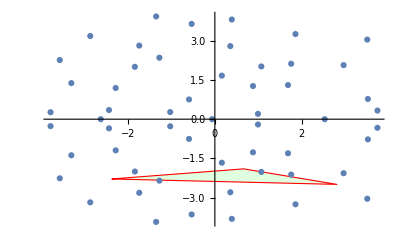

```mathematica
{m,s}={55,4};
{p1,p2,p3}=3RandomComplex[{-1-I,1+I},{3}];
A=RandomReal[{-1,1},{m,m}];
λ=Eigenvalues[A];
ListPlot[ReIm[λ],Prolog->{LightGreen,EdgeForm[Red], Polygon[ReIm[{p1,p2,p3}]]}]
S=Orthogonalize[RandomReal[{-1,1},{s,m}]]ᵀ;
Res[λ_]:=Inverse[A-λ IdentityMatrix[m]]
Clear[F1,F2,F3]
MaxOrder=13;
{F1[0],F2[0],F3[0]}=Map[LinearSolve[A-# IdentityMatrix[m],S]&,{p1,p2,p3}];
Do[
{F1[i],F2[i],F3[i]}={
LinearSolve[A-p1 IdentityMatrix[m],F1[i-1]],
LinearSolve[A-p2 IdentityMatrix[m],F2[i-1]],
LinearSolve[A-p3 IdentityMatrix[m],F3[i-1]]},
{i, 1,MaxOrder}]
```

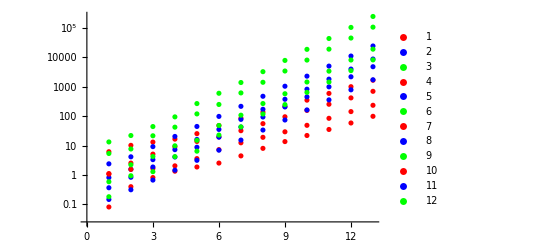

```mathematica
jVal=4;
iVal=5;
ListLogPlot[{
Table[Norm[F1[i]],{i,1,MaxOrder}],
Table[Norm[F2[i]],{i,1,MaxOrder}],
Table[Norm[F3[i]],{i,1,MaxOrder}],
Table[Norm[F1[i]⟦All,jVal⟧],{i,1, MaxOrder}],Table[Norm[F2[i]⟦All,jVal⟧],{i,1, MaxOrder}],
Table[Norm[F3[i]⟦All,jVal⟧],{i,1, MaxOrder}],
Table[Norm[F1[i]⟦iVal,All⟧],{i,1, MaxOrder}],Table[Norm[F2[i]⟦iVal,All⟧],{i,1, MaxOrder}],
Table[Norm[F3[i]⟦iVal,All⟧],{i,1, MaxOrder}],
Table[Norm[F1[i]⟦iVal,jVal⟧],{i,1, MaxOrder}],Table[Norm[F2[i]⟦iVal,jVal⟧],{i,1, MaxOrder}],
Table[Norm[F3[i]⟦iVal,jVal⟧],{i,1, MaxOrder}]
},
PlotStyle->{Red, Blue, Green},
PlotLegends->Range[1,100]]
```

## Interpolation in Mathematica

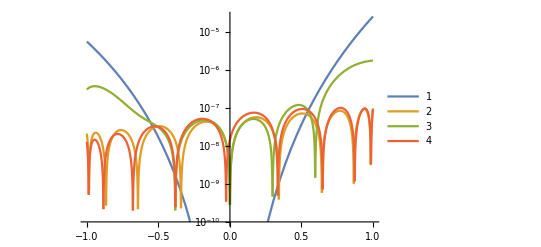

```mathematica
Needs["FunctionApproximations`"]
Clear[m,n,f,p,r,e]
{m,n}={4,4};
f[x_]:=Cos[x] E^x
p[x_]=N[PadeApproximant[f[x],{x,0,{m,n}}]];
r[x_]=RationalInterpolation[f[x],{x,m,n},{x,-1.0,1}];
e[x_]=EconomizedRationalApproximation[f[x],{x,{-1,1},m,n}];
{xs,{mm[x_],err}}=MiniMaxApproximation[f[x],{x,{-1,1},m,n}];
LogPlot[{Abs[f[x]-p[x]],Abs[f[x]-r[x]],Abs[f[x]-e[x]],Abs[f[x]-mm[x]]},{x,-1,1},
PlotLegends->Automatic]
```

```mathematica
?Interpolation
```